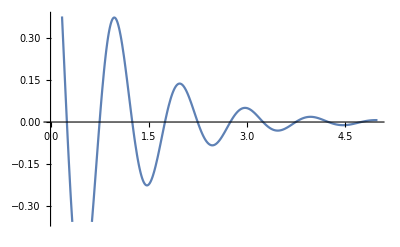

```mathematica
Plot[E^(-t)*Cos[2*Pi*t],{t,0,5}]
```

8.1

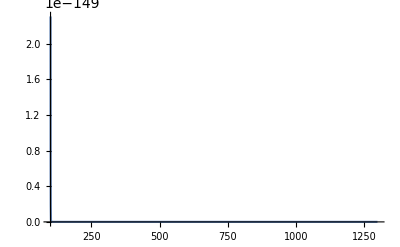

```mathematica
b=8.1
Plot[1/2*E^((-b/2-Sqrt[b^2-64]/2)*t)+1/2*E^((-b/2+Sqrt[b^2-64]/2)*t), {t, 100, 1300}]
```

```mathematica
AnimatePlot[(2+3*I)/t,{t,0.1, 40}]
```

ComplexPlot::plld: Corners for t in {t,0.1,40} must have distinct machine-precision real and imaginary parts.

ComplexPlot[(2+3 ⅈ)/t,{t,0.1,40}]

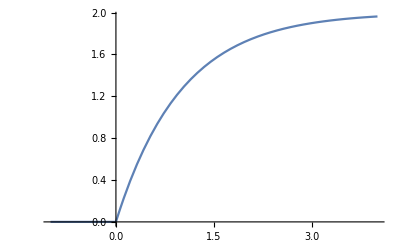

```mathematica
Plot[2*UnitStep[t]*(1-E^(-t)),{t, -1,4}]
```

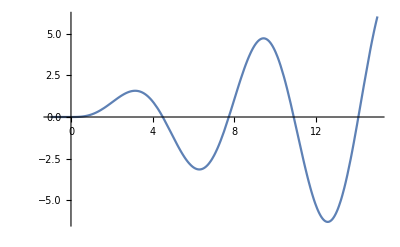

```mathematica
Plot[UnitStep[t]/2*(Sin[t]-t*Cos[t]), {t, -1,15}]
```

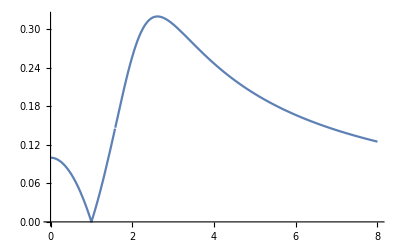

```mathematica
Plot[Abs[((w*I)^2+1)/(((w*I)^2+2*w*I+5)*(w*I+2))], {w, 0, 8}]
```

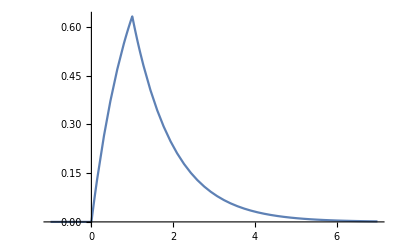

```mathematica
Plot[Integrate[(E^(-q))*(UnitStep[t-q]-UnitStep[t-q-1]), {q,0,t}], {t,-1,7}]
```

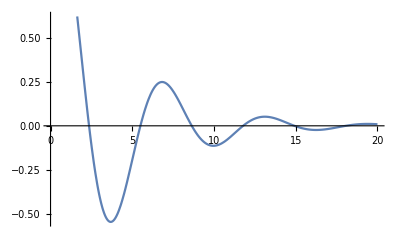

```mathematica
Plot[Sqrt[2]*E^(-t/4)*Cos[t-Pi/4],{t, 0, 20}]
```